## Loading

```mathematica
(* Ввод путей до .npy файлов
valPath - путь к исходным кубоидам
genPath - путь к сгенерированным кубоидам *)
valPath =SystemDialogInput["FileOpen","val_cuboids_spheresRVE.npy",WindowTitle->"val_cuboids_spheresRVE"];
genPath = SystemDialogInput["FileOpen","gen_cuboids_spheresRVE.npy",WindowTitle->"gen_cuboids_spheresRVE"];
```

```mathematica
(* Получаем массивы из .npy файлов *)
SetDirectory[NotebookDirectory[]]
<<NumPyArray` (* Импорт пакета для загрузки .npy файлов *)
valCuboids = ReadNumPyArray[valPath];
genCuboids = ReadNumPyArray[genPath];
```

C:\Users\Mikhail\OneDrive\WORK\MATHEMATICAWorking\Женя К

ReadNumPyArray::shdw: Symbol ReadNumPyArray appears in multiple contexts {NumPyArray`,Global`}; definitions in context NumPyArray` may shadow or be shadowed by other definitions.

```mathematica
(* Внимательно смотрим на форму массивов:
форма valCuboids - {m, n_x, n_y, n_z}, где
	m - количество исходных кубоидов
	n_x, n_y и n_z - количество вокселей вдоль осей X, Y и Z соотвутственно

форма genCuboids - {m_gen, m, n_x, n_y, n_z}, где
	m_gen - количество сгенерированных кубоидов для какого-то из m исходных
	m - количество исходных кубоидов
	n_x, n_y и n_z - количество вокселей вдоль осей X, Y и Z соотвутственно
		 *)
Dimensions[valCuboids]
Dimensions[genCuboids]
```

{100,64,64,64}

{100,100,64,64,64}

## Transforming into a continuous area

## Visualisation

```mathematica
Graphics3D[{LightYellow,Lighting->"Neutral",First@Last@Reap[MapIndexed[If[#==1,Sow[Cuboid[#2]]]&,valCuboids[[1,All,All,All]],-1]]},AxesLabel->{"StyleBox[\"X\",FontSize->16,FontWeight->\"Bold\"]","StyleBox[\"Y\",FontSize->16,FontWeight->\"Bold\"]","StyleBox[\"Z\",FontSize->16,FontWeight->\"Bold\"]"},ViewPoint->{-2.4,1.4,1.6},Axes->False,Boxed->True]
```

-Graphics3D-

```mathematica
basic=ResourceFunction["ArrayRotations"][vox[[1,1,All,All]]]
```

{{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},63},{1},{1},{1},{1},{1},{1},{1}}
 |  |  |  |

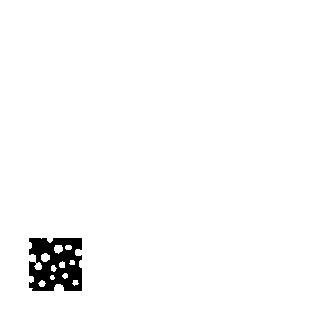
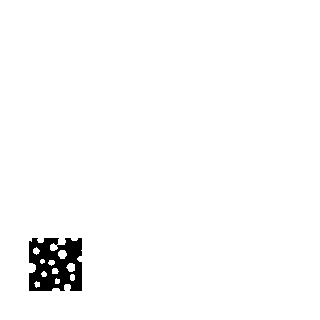
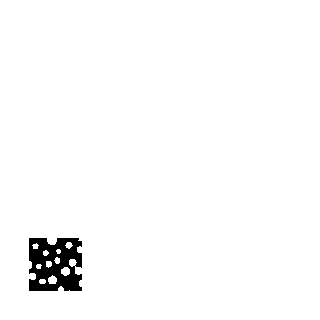
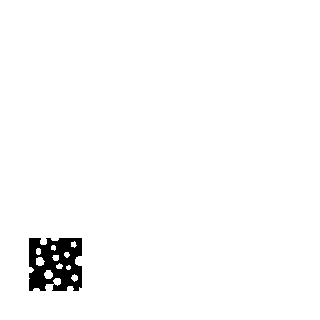
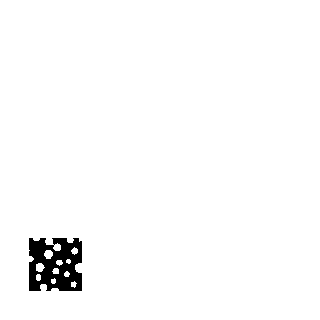
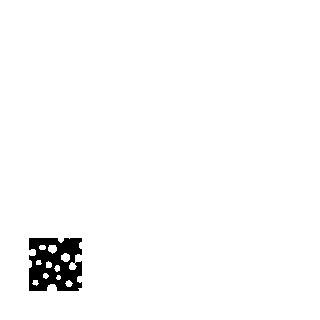
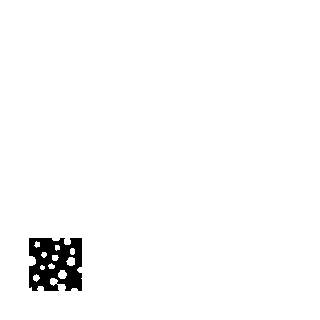
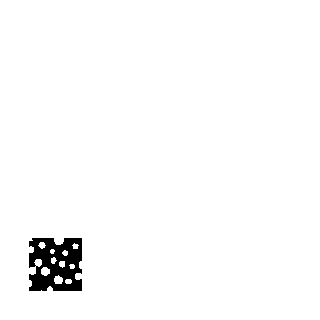

```mathematica
ArrayPlot[#,PixelConstrained->5]&/@basic
```

## Convert to FEM

#### Single structure

```mathematica
workdir=SystemDialogInput["Directory",Directory[]];
With[{mgen=1,m=1},rrb=Image3D[genCuboids[[mgen,m]]];uniquenumber="mgen_"<>ToString[mgen]<>"_m_"<>ToString[m];directoryname=workdir<>"mgen_"<>ToString[mgen]<>"_m_"<>ToString[m]];
x0=y0=z0=0;
xA=yA=zA=2;
rrbm=RegionResize[ImageMesh[rrb,Method->"DualMarchingCubes"],{{x0,xA},{y0,yA},{z0,zA}}];
p=1-Volume[rrbm]/((xA-x0)*(yA-y0)*(zA-z0));
```

0.210135

```mathematica
rrn=ColorNegate[rrb];
rrnm=RegionResize[ImageMesh[rrn,Method->"DualMarchingCubes"],{{x0,xA},{y0,yA},{z0,zA}}];
```

```mathematica
Needs["NDSolve`FEM`"];
(*inclusionsmesh=ToElementMesh[rrnm];*)
matrixmesh=ToElementMesh[rrbm,"RegionHoles"->RandomPoint[rrnm,5]];
```

```mathematica
Needs["MeshTools`"];
assembly=AddMeshMarkers[matrixmesh,"MeshElementsMarker"->2];
twophaseflag=False;
```

```mathematica
assemblypic=Rasterize[Show[assembly["Wireframe"["MeshElement"->"MeshElements","MeshElementStyle"->FaceForm/@{Yellow,Orange}]],Boxed->False,ViewPoint->{1.25,-1.5,1.7},Axes->True,LabelStyle->20,AxesStyle->Directive[Black,Thick,FontFamily->"Cambria"],AxesLabel->{"\!\(\*
StyleBox[\"X\",\nFontSize->24,\nFontWeight->\"Bold\"]\)","\!\(\*
StyleBox[\"Y\",\nFontSize->24,\nFontWeight->\"Bold\"]\)","\!\(\*
StyleBox[\"Z\",\nFontSize->24,\nFontWeight->\"Bold\"]\)"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ImageSize->Large],ImageResolution->150];
```

False

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"MeshPrepare_v1.1.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"MeshExporter_v3.6.2_force_Zaxis_NoDirChoose.nb"}]]
```

Number of elements in inclusions phase 0

Number of elements in matrix phase 560091

Total number of elements 560091

Number of nodes 837571

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 4958, 5469

Length of z0nodes and zAnodes = 2721, 2847

Text expressions memorized. Ready to create INP file.

C:\Users\Mikhail\OneDrive\WORK\MATHEMATICAWorking\Женя К\Test

#### Multiple Structures

```mathematica
workdir=SystemDialogInput["Directory",Directory[],WindowTitle->"Choose working directory"];
Needs["NDSolve`FEM`"];
Needs["MeshTools`"];

For[mgen=1;m=1,mgen<=5,mgen++,(* Здесь указано сколько структур с разным mgen подряд будет сгенерировано *)
Print[];
rrb=Image3D[genCuboids[[mgen,m]]];uniquenumber="mgen_"<>ToString[mgen]<>"_m_"<>ToString[m];directoryname=workdir<>"mgen_"<>ToString[mgen]<>"_m_"<>ToString[m];
Print[directoryname];
x0=y0=z0=0;
xA=yA=zA=2;
rrbm=RegionResize[ImageMesh[rrb,Method->"DualMarchingCubes"],{{x0,xA},{y0,yA},{z0,zA}}];
p=1-Volume[rrbm]/((xA-x0)*(yA-y0)*(zA-z0));
rrn=ColorNegate[rrb];
rrnm=RegionResize[ImageMesh[rrn,Method->"DualMarchingCubes"],{{x0,xA},{y0,yA},{z0,zA}}];

(*inclusionsmesh=ToElementMesh[rrnm];*)
matrixmesh=ToElementMesh[rrbm,"RegionHoles"->RandomPoint[rrnm,5]];

assembly=AddMeshMarkers[matrixmesh,"MeshElementsMarker"->2];
twophaseflag=False;

assemblypic=Rasterize[Show[assembly["Wireframe"["MeshElement"->"MeshElements","MeshElementStyle"->FaceForm/@{Yellow,Orange}]],Boxed->False,ViewPoint->{1.25,-1.5,1.7},Axes->True,LabelStyle->20,AxesStyle->Directive[Black,Thick,FontFamily->"Cambria"],AxesLabel->{"\!\(\*
StyleBox[\"X\",\nFontSize->24,\nFontWeight->\"Bold\"]\)","\!\(\*
StyleBox[\"Y\",\nFontSize->24,\nFontWeight->\"Bold\"]\)","\!\(\*
StyleBox[\"Z\",\nFontSize->24,\nFontWeight->\"Bold\"]\)"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ImageSize->Large],ImageResolution->150];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"MeshPrepare_v1.1.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"MeshExporter_v3.6.2_force_Zaxis_NoDirChoose.nb"}]];

];
```

Number of elements in inclusions phase 0

Number of elements in matrix phase 562800

Total number of elements 562800

Number of nodes 839497

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 4947, 5465

Length of z0nodes and zAnodes = 2722, 2846

Text expressions memorized. Ready to create INP file.

CreateDirectory::eexist: B:\AbaqusWorking\Generated\Test\mgen_1_m_1 already exists.

B:\AbaqusWorking\Generated\Test\mgen_1_m_1

Number of elements in inclusions phase 0

Number of elements in matrix phase 561859

Total number of elements 561859

Number of nodes 841146

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 5168, 5632

Length of z0nodes and zAnodes = 2807, 2803

Text expressions memorized. Ready to create INP file.

B:\AbaqusWorking\Generated\Test\mgen_2_m_1

ToElementMesh::femimq: The element mesh has insufficient quality of 0.. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

Number of elements in inclusions phase 0

Number of elements in matrix phase 546353

Total number of elements 546353

Number of nodes 112756

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 5223, 5343

Length of z0nodes and zAnodes = 2833, 2845

Text expressions memorized. Ready to create INP file.

B:\AbaqusWorking\Generated\Test\mgen_3_m_1

Number of elements in inclusions phase 0

Number of elements in matrix phase 545099

Total number of elements 545099

Number of nodes 820023

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 4955, 5568

Length of z0nodes and zAnodes = 2663, 2546

Text expressions memorized. Ready to create INP file.

B:\AbaqusWorking\Generated\Test\mgen_4_m_1

#### MultipleMultiple Structures

```mathematica
workdir=SystemDialogInput["Directory",Directory[],WindowTitle->"Choose working directory"];
Needs["NDSolve`FEM`"];
Needs["MeshTools`"];

For[m=1,m<=5,m++,(* Здесь указано сколько структур с разным mgen подряд будет сгенерировано *)
For[mgen=1,mgen<=5,mgen++,
Print[];
rrb=Image3D[genCuboids[[mgen,m]]];uniquenumber="m_"<>ToString[m]<>"_mgen_"<>ToString[mgen];directoryname=workdir<>"m_"<>ToString[m]<>"_mgen_"<>ToString[mgen];
Print[directoryname];
x0=y0=z0=0;
xA=yA=zA=2;
rrbm=RegionResize[ImageMesh[rrb,Method->"DualMarchingCubes"],{{x0,xA},{y0,yA},{z0,zA}}];
p=1-Volume[rrbm]/((xA-x0)*(yA-y0)*(zA-z0));
rrn=ColorNegate[rrb];
rrnm=RegionResize[ImageMesh[rrn,Method->"DualMarchingCubes"],{{x0,xA},{y0,yA},{z0,zA}}];

(*inclusionsmesh=ToElementMesh[rrnm];*)
matrixmesh=ToElementMesh[rrbm,"RegionHoles"->RandomPoint[rrnm,5]];

assembly=AddMeshMarkers[matrixmesh,"MeshElementsMarker"->2];
twophaseflag=False;

assemblypic=Rasterize[Show[assembly["Wireframe"["MeshElement"->"MeshElements","MeshElementStyle"->FaceForm/@{Yellow,Orange}]],Boxed->False,ViewPoint->{1.25,-1.5,1.7},Axes->True,LabelStyle->20,AxesStyle->Directive[Black,Thick,FontFamily->"Cambria"],AxesLabel->{"\!\(\*
StyleBox[\"X\",\nFontSize->24,\nFontWeight->\"Bold\"]\)","\!\(\*
StyleBox[\"Y\",\nFontSize->24,\nFontWeight->\"Bold\"]\)","\!\(\*
StyleBox[\"Z\",\nFontSize->24,\nFontWeight->\"Bold\"]\)"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ImageSize->Large],ImageResolution->150];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"MeshPrepare_v1.1.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"MeshExporter_v3.6.2_force_Zaxis_NoDirChoose.nb"}]];

];];
```

Number of elements in inclusions phase 0

Number of elements in matrix phase 562800

Total number of elements 562800

Number of nodes 839497

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 4947, 5465

Length of z0nodes and zAnodes = 2722, 2846

Text expressions memorized. Ready to create INP file.

CreateDirectory::eexist: B:\AbaqusWorking\Generated\Test\mgen_1_m_1 already exists.

B:\AbaqusWorking\Generated\Test\mgen_1_m_1

Number of elements in inclusions phase 0

Number of elements in matrix phase 561859

Total number of elements 561859

Number of nodes 841146

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 5168, 5632

Length of z0nodes and zAnodes = 2807, 2803

Text expressions memorized. Ready to create INP file.

B:\AbaqusWorking\Generated\Test\mgen_2_m_1

ToElementMesh::femimq: The element mesh has insufficient quality of 0.. A quality estimate below 0. may be caused by a wrong ordering of element incidents or self-intersecting elements.

Number of elements in inclusions phase 0

Number of elements in matrix phase 546353

Total number of elements 546353

Number of nodes 112756

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 5223, 5343

Length of z0nodes and zAnodes = 2833, 2845

Text expressions memorized. Ready to create INP file.

B:\AbaqusWorking\Generated\Test\mgen_3_m_1

Number of elements in inclusions phase 0

Number of elements in matrix phase 545099

Total number of elements 545099

Number of nodes 820023

(* Top and Bottom nodes of Matrix *)

Length of y0nodes and yAnodes = 4955, 5568

Length of z0nodes and zAnodes = 2663, 2546

Text expressions memorized. Ready to create INP file.

B:\AbaqusWorking\Generated\Test\mgen_4_m_1